```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0
```

r>0&&m∈Integers&&n∈Integers&&s>0

```mathematica
f[r_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}}-0*IdentityMatrix[2]*I*r^p;f[r]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

```mathematica
En=E0+I*Ga;En=.
```

```mathematica
VV[x_]:=Exp[I*Integrate[r^p-En,{r,0,x}]]
```

```mathematica
u=  {F[x],G[x]}*x^s
```

{x^(-1+m) F[x],x^(-1+m) G[x]}

```mathematica
p=2;
```

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[(-D[u,x]+r'[x]*f[r[x]].u)*x^-s]]],{x^n,a[n],b[n]}]
```

{(2 F[x])/x-(2 m F[x])/x+(ⅈ G[x])/x^4-(ⅈ En G[x])/x^2-F'[x],(ⅈ F[x])/x^4-(ⅈ En F[x])/x^2+G[x]/x-G'[x]}

```mathematica
f2[r_]:={{1,I En -I x^2},{I En - I x^2,(1-2 m)/x }};f2[r]//MatrixForm
```

(1 | ⅈ En-ⅈ x^2
ⅈ En-ⅈ x^2 | (1-2 m)/x)

```mathematica
u=  {a[n]*x^(n),b[n]*x^(n)}*x^S
```

{x^(n+S) a[n],x^(n+S) b[n]}

```mathematica
r[x_]:=1/x;
```

```mathematica
s=m-1;
```

```mathematica
g2=Collect[Expand[Simplify[Expand[(-D[u,x]+r'[x]*f2[r[x]].u)*x^(3-S)*{1,-1}]]],{x^n,a[n],b[n]}]
```

{x^n ((-x-n x^2-S x^2) a[n]+(-ⅈ En x+ⅈ x^3) b[n]),x^n ((ⅈ En x-ⅈ x^3) a[n]+(1-2 m+n x^2+S x^2) b[n])}

```mathematica
g3=Table[Simplify[Sum[D[g2,{x,n2}]/n2!,{n,0,10}]/.x->0],{n2,0,10}];g3//MatrixForm
```

(0 | (1-2 m) b[0]
-a[0]-ⅈ En b[0] | ⅈ En a[0]+b[1]-2 m b[1]
-S a[0]-a[1]-ⅈ En b[1] | ⅈ En a[1]+S b[0]+b[2]-2 m b[2]
-a[1]-S a[1]-a[2]+ⅈ b[0]-ⅈ En b[2] | -ⅈ a[0]+ⅈ En a[2]+b[1]+S b[1]+b[3]-2 m b[3]
-2 a[2]-S a[2]-a[3]+ⅈ b[1]-ⅈ En b[3] | -ⅈ a[1]+ⅈ En a[3]+2 b[2]+S b[2]+b[4]-2 m b[4]
-3 a[3]-S a[3]-a[4]+ⅈ b[2]-ⅈ En b[4] | -ⅈ a[2]+ⅈ En a[4]+3 b[3]+S b[3]+b[5]-2 m b[5]
-4 a[4]-S a[4]-a[5]+ⅈ b[3]-ⅈ En b[5] | -ⅈ a[3]+ⅈ En a[5]+4 b[4]+S b[4]+b[6]-2 m b[6]
-5 a[5]-S a[5]-a[6]+ⅈ b[4]-ⅈ En b[6] | -ⅈ a[4]+ⅈ En a[6]+5 b[5]+S b[5]+b[7]-2 m b[7]
-6 a[6]-S a[6]-a[7]+ⅈ b[5]-ⅈ En b[7] | -ⅈ a[5]+ⅈ En a[7]+6 b[6]+S b[6]+b[8]-2 m b[8]
-7 a[7]-S a[7]-a[8]+ⅈ b[6]-ⅈ En b[8] | -ⅈ a[6]+ⅈ En a[8]+7 b[7]+S b[7]+b[9]-2 m b[9]
-8 a[8]-S a[8]-a[9]+ⅈ b[7]-ⅈ En b[9] | -ⅈ a[7]+ⅈ En a[9]+8 b[8]+S b[8]+b[10]-2 m b[10])

```mathematica
a[0]=1; b[0]=0;a[1]=-ⅈ En a[0];b[1]=En/(2 m);a[2]=-ⅈ En a[1]/2-En b[1]/2;b[2]=-1/(1+2 m)(-En a[1]+ⅈ En b[1]);
```

```mathematica
Simplify[I*(ⅈ a[n]-ⅈ En a[n+2]-(n+3) a[n+3]+b[n]-En b[n+2])+a[n]-En a[n+2]-ⅈ b[n]+ⅈ En b[n+2]+(n+2) b[n+3]+2 m b[n+3]]
```

-ⅈ (3+n) a[3+n]+(2+2 m+n) b[3+n]

```mathematica
b[n_]:=ⅈ (n) a[n]/(-1+2 m+n)
```

```mathematica
Collect[ⅈ a[n]-ⅈ En a[n+2]-(n+3) a[n+3]+b[n]-En b[n+2],{a[n],a[n+3],a[n+2]}]/.n->n-3
```

(ⅈ+(ⅈ (-3+n))/(-4+2 m+n)) a[-3+n]+(-ⅈ En-(ⅈ En (-1+n))/(-2+2 m+n)) a[-1+n]-n a[n]

```mathematica
a[n_]:=1/n*((ⅈ+(ⅈ (-3+n))/(-4+2 m+n)) a[-3+n]+(-ⅈ En-(ⅈ En (-1+n))/(-2+2 m+n)) a[-1+n])
```

```mathematica
b[2]
```

-(ⅈ En^2+(ⅈ En^2)/(2 m))/(1+2 m)

```mathematica
U[En_,m_,nN_]:=Module[{U,te},
U={{1,0},{-ⅈ En,En/(2 m)},{-En^2/2-En^2/(4 m),-(ⅈ En^2+(ⅈ En^2)/(2 m))/(1+2 m)}};

For[n=3,n<nN,n++,
te=1/n*((ⅈ+(ⅈ (-3+n))/(-4+2 m+n)) U[[-2+n,1]]+(-ⅈ En-(ⅈ En (-1+n))/(-2+2 m+n)) U[[n,1]]);
AppendTo[U,{te,ⅈ (n) te/(-1+2 m+n)}];
];
{1,1}*Exp[-I*Integrate[r^p-En,{r,0,x}]];
 Expand[ Sum[U[[n+1]]*x^n,{n ,0,nN-1}]*x^(-1+m)]

]
```

```mathematica
Simplify[U[En,m,15]-Table[{a[n],b[n]},{n,0,14}]]
```

$Aborted

```mathematica
U[10,2,5]//N//MatrixForm
```

(x-(0.+10. ⅈ) x^2-62.5 x^3+(0.+292. ⅈ) x^4+1098.13 x^5
2.5 x^2-(0.+25. ⅈ) x^3-146. x^4+(0.+627.5 ⅈ) x^5)

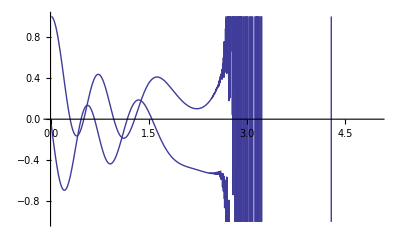

```mathematica
G=U[5+I*0.25,1,250][[1]];Plot[{Re[#],Im[#]}&[G],{x,0,5},PlotRange->{-1,1}]
```

```mathematica
G
```

{{Re[ⅇ^(-ⅈ (-En x+x^3/3)) (x-10 ⅈ x^2-(125 x^3)/2+292 ⅈ x^4+(8785 x^5)/8)],Re[ⅇ^(-ⅈ (-En x+x^3/3)) ((5 x^2)/2-25 ⅈ x^3-146 x^4+(1255 ⅈ x^5)/2)]},{Im[ⅇ^(-ⅈ (-En x+x^3/3)) (x-10 ⅈ x^2-(125 x^3)/2+292 ⅈ x^4+(8785 x^5)/8)],Im[ⅇ^(-ⅈ (-En x+x^3/3)) ((5 x^2)/2-25 ⅈ x^3-146 x^4+(1255 ⅈ x^5)/2)]}}

```mathematica
VV[x]
```

ⅇ^(ⅈ (-En x+x^3/3))